```mathematica
WordNum=RandomInteger[{5,5}];MeanNum=RandomInteger[{5,5}];PlayerNum=RandomInteger[{5,5}];RefinementThreshold=0.7;
```

```mathematica
(*WMMs=(#->RandomReal[1,{WordNum,MeanNum}])&/@Range[4];*)
```

```mathematica
RescaleRow[row_]:=row/Total[row]
```

```mathematica
WMMs=(#->Table[RescaleRow[RandomReal[1,MeanNum]],WordNum])&/@Range[PlayerNum-1];
```

```mathematica
WMMs
```

{1→{{0.0852959,0.036525,0.0855914,0.420023,0.372565},{0.182501,0.259112,0.179699,0.216182,0.162506},{0.13363,0.310371,0.186998,0.275657,0.0933445},{0.235122,0.286797,0.234491,0.0434459,0.200144},{0.225427,0.0727704,0.305048,0.187964,0.208791}},2→{{0.46921,0.0729372,0.276849,0.0543801,0.126623},{0.258013,0.275858,0.0693516,0.0887552,0.308022},{0.247371,0.0194114,0.27756,0.256184,0.199473},{0.198432,0.232337,0.0386868,0.333715,0.196829},{0.245564,0.354572,0.206969,0.10242,0.0904748}},3→{{0.0158234,0.322268,0.246907,0.272081,0.142921},{0.124956,0.248312,0.261862,0.158609,0.20626},{0.352034,0.093659,0.139995,0.367475,0.046838},{0.14533,0.0750717,0.140878,0.237421,0.4013},{0.263059,0.253874,0.154969,0.126874,0.201224}},4→{{0.306722,0.0843706,0.0991735,0.250681,0.259053},{0.12247,0.315461,0.269165,0.253207,0.039697},{0.221039,0.188037,0.340424,0.0101882,0.240311},{0.0313207,0.259904,0.231201,0.213951,0.263624},{0.15579,0.0579057,0.17718,0.330662,0.278462}}}

```mathematica
Table[If[i==Max[(1/.InitialWMMs)[[row]]],0.8,0.2/MeanNum],{row,WordNum},{i,(1/.InitialWMMs)[[row]]}]
```

{{0.04,0.04,0.04,0.8,0.04},{0.04,0.8,0.04,0.04,0.04},{0.04,0.8,0.04,0.04,0.04},{0.04,0.8,0.04,0.04,0.04},{0.04,0.04,0.8,0.04,0.04}}

```mathematica
GetBestWordsForLang[1]
```

{4,2,2,2,3}

```mathematica
WMMs=InitialWMMs/.{(4->_):>(4->Table[If[i==j,0.8,0.2/MeanNum],{i,WordNum},{j,MeanNum}])}
```

{1→{{0.0852959,0.036525,0.0855914,0.420023,0.372565},{0.182501,0.259112,0.179699,0.216182,0.162506},{0.13363,0.310371,0.186998,0.275657,0.0933445},{0.235122,0.286797,0.234491,0.0434459,0.200144},{0.225427,0.0727704,0.305048,0.187964,0.208791}},2→{{0.0852959,0.036525,0.0855914,0.420023,0.372565},{0.182501,0.259112,0.179699,0.216182,0.162506},{0.13363,0.310371,0.186998,0.275657,0.0933445},{0.235122,0.286797,0.234491,0.0434459,0.200144},{0.225427,0.0727704,0.305048,0.187964,0.208791}},3→{{0.0852959,0.036525,0.0855914,0.420023,0.372565},{0.182501,0.259112,0.179699,0.216182,0.162506},{0.13363,0.310371,0.186998,0.275657,0.0933445},{0.235122,0.286797,0.234491,0.0434459,0.200144},{0.225427,0.0727704,0.305048,0.187964,0.208791}},4→{{0.8,0.04,0.04,0.04,0.04},{0.04,0.8,0.04,0.04,0.04},{0.04,0.04,0.8,0.04,0.04},{0.04,0.04,0.04,0.8,0.04},{0.04,0.04,0.04,0.04,0.8}},5→{{0.8,0.04,0.04,0.04,0.04},{0.04,0.8,0.04,0.04,0.04},{0.04,0.04,0.8,0.04,0.04},{0.04,0.04,0.04,0.8,0.04},{0.04,0.04,0.04,0.04,0.8}}}

```mathematica
AppendTo[WMMs,5->Table[If[i==j,0.8,0.2/MeanNum],{i,WordNum},{j,MeanNum}]]
```

{1→{{0.0852959,0.036525,0.0855914,0.420023,0.372565},{0.182501,0.259112,0.179699,0.216182,0.162506},{0.13363,0.310371,0.186998,0.275657,0.0933445},{0.235122,0.286797,0.234491,0.0434459,0.200144},{0.225427,0.0727704,0.305048,0.187964,0.208791}},2→{{0.0852959,0.036525,0.0855914,0.420023,0.372565},{0.182501,0.259112,0.179699,0.216182,0.162506},{0.13363,0.310371,0.186998,0.275657,0.0933445},{0.235122,0.286797,0.234491,0.0434459,0.200144},{0.225427,0.0727704,0.305048,0.187964,0.208791}},3→{{0.0852959,0.036525,0.0855914,0.420023,0.372565},{0.182501,0.259112,0.179699,0.216182,0.162506},{0.13363,0.310371,0.186998,0.275657,0.0933445},{0.235122,0.286797,0.234491,0.0434459,0.200144},{0.225427,0.0727704,0.305048,0.187964,0.208791}},4→{{0.0852959,0.036525,0.0855914,0.420023,0.372565},{0.182501,0.259112,0.179699,0.216182,0.162506},{0.13363,0.310371,0.186998,0.275657,0.0933445},{0.235122,0.286797,0.234491,0.0434459,0.200144},{0.225427,0.0727704,0.305048,0.187964,0.208791}},5→{{0.8,0.04,0.04,0.04,0.04},{0.04,0.8,0.04,0.04,0.04},{0.04,0.04,0.8,0.04,0.04},{0.04,0.04,0.04,0.8,0.04},{0.04,0.04,0.04,0.04,0.8}}}

```mathematica
InitialWMMs=WMMs;
```

```mathematica
GamesTally=ConstantArray[{0,0,0},PlayerNum]; (*{GamesWon as Speaker, GamesWon as Listener, GamesPlayed}*)
```

```mathematica
UpdateWord[word_,lambda_,meaningid_,gameWon_]:=Module[{
correctMeaningProb=word[[meaningid]],
sign=If[gameWon,1,-1],
n=Length[word]
},
Return[RescaleRow[Table[
If[eachmeaning!=meaningid,
newMeaning=word[[eachmeaning]]-Divide[sign*lambda,n-1];
If[newMeaning<0,0,If[newMeaning>1,1,newMeaning]],
newMeaning=correctMeaningProb+sign*lambda;
If[newMeaning>1,1,If[newMeaning<0,0,newMeaning]]],
{eachmeaning,1,Length[word]}]]]
]
```

```mathematica
UpdateMeaning[meaning_,lambda_,wordid_,gameWon_]:=Module[{
correctWord=meaning[[wordid]],
sign=If[gameWon,1,-1],
n=Length[meaning]
},
Return[Table[If[eachword!=wordid,
newword=meaning[[eachword]]-Divide[sign*lambda,n-1];
If[newword<0,0,If[newword>1,1,newword]],
newword=correctWord+sign*lambda;
If[newword>1,1,If[newword<0,0,newword]]],
{eachword,1,Length[meaning]}]]
]
```

```mathematica
PlayNormalGame[L0_,L1_]:=Block[{
SpeakerWMM = L0 /. WMMs,
ListenerWMM=L1/.WMMs,
GameMeaningID=RandomInteger[{1,MeanNum}],
Lambda=0.1
},
Print["Playing normal Game"];
GameMeaning=SpeakerWMM[[All,GameMeaningID]];
If[Total[GameMeaning]==0,GameMeaning=ConstantArray[1/MeanNum,WordNum]];
SpokenWordID=RandomChoice[GameMeaning->Range[WordNum]];
InterpretedMeaningID=RandomChoice[ListenerWMM[[SpokenWordID]]->Range[MeanNum]];
GameWon=InterpretedMeaningID==GameMeaningID;

(*Print[StringForm["`` => L0: `` => L1: `` |==> ``... Updating `` by ``",UniversalMeanings[[GameMeaningID]],AllWords[[SpokenWordID]], UniversalMeanings[[InterpretedMeaningID]], GameWon, If[GameWon, {{"s", L0},{"l",L1}}, If[SpeakerCorrect,{"l",L1},If[ListenerCorrect,{"s",L0}, "none"]]],Lambda]];*)

ListenerWMM[[SpokenWordID]]=UpdateWord[ListenerWMM[[SpokenWordID]],Lambda,InterpretedMeaningID,GameWon];
SpeakerWMM[[All,GameMeaningID]]=UpdateMeaning[SpeakerWMM[[All,GameMeaningID]],Lambda,SpokenWordID,GameWon];
SpeakerWMM=Table[RescaleRow[row],{row,SpeakerWMM}];

WMMs = WMMs/.{(L0->_):>L0->SpeakerWMM, (L1->_):>L1->ListenerWMM};
Return[GameWon]
];
```

```mathematica
PlayTeacherGame[L0_,L1_]:=Block[{
TeacherWMM = L0 /. WMMs,
StudentWMM=L1/.WMMs,
GameMeaningID=RandomInteger[{1,MeanNum}],
Lambda=0.1
},
Print["Playing teacher Game"];
GameMeaning=TeacherWMM[[All,GameMeaningID]];
If[Total[GameMeaning]==0,GameMeaning=ConstantArray[1/MeanNum,WordNum]];
SpokenWordID=RandomChoice[GameMeaning->Range[WordNum]];

(*Print[StringForm["`` => L0: `` => L1: `` |==> ``... Updating `` by ``",UniversalMeanings[[GameMeaningID]],AllWords[[SpokenWordID]], UniversalMeanings[[InterpretedMeaningID]], GameWon, If[GameWon, {{"s", L0},{"l",L1}}, If[SpeakerCorrect,{"l",L1},If[ListenerCorrect,{"s",L0}, "none"]]],Lambda]];*)

StudentWMM[[SpokenWordID]]=UpdateWord[StudentWMM[[SpokenWordID]],Lambda,GameMeaningID,True];
TeacherWMM[[All,GameMeaningID]]=UpdateMeaning[TeacherWMM[[All,GameMeaningID]],Lambda,SpokenWordID,True];
TeacherWMM=Table[RescaleRow[row],{row,TeacherWMM}];

WMMs = WMMs/.{(L0->_):>L0->TeacherWMM, (L1->_):>L1->StudentWMM};
Return[True]
];
```

```mathematica
PlayBroadcastGame[L0_,L1_]:=Block[{
BroadcasterWMM=L0/.WMMs,
ListenersList=RandomSample[DeleteCases[Range[PlayerNum],1],RandomInteger[{2,PlayerNum-1}]],
GameMeaningID=RandomInteger[{1,MeanNum}],
Lambda=0.1},
Print["Playing broadcast Game"];
GameMeaning=BroadcasterWMM[[All,GameMeaningID]];
If[Total[GameMeaning]==0,GameMeaning=ConstantArray[1/MeanNum,WordNum]];
SpokenWordID=RandomChoice[GameMeaning->Range[WordNum]];

GamesResult=Table[
ListenerWMM=listener/.WMMs;
InterpretedMeaningID=RandomChoice[ListenerWMM[[SpokenWordID]]->Range[MeanNum]];
GameWon=InterpretedMeaningID==GameMeaningID;
ListenerWMM[[SpokenWordID]]=UpdateWord[ListenerWMM[[SpokenWordID]],Lambda,InterpretedMeaningID,GameWon];
WMMs=WMMs/.{(listener->_):>listener->ListenerWMM};
GameWon,{listener,ListenersList}];

Lambda=((2*Total[Boole[GamesResult]]/Length[GamesResult])-1)*Lambda;

BroadcasterWMM[[All,GameMeaningID]]=UpdateMeaning[BroadcasterWMM[[All,GameMeaningID]],Lambda,SpokenWordID,True];
BroadcasterWMM=Table[RescaleRow[row],{row,BroadcasterWMM}];

WMMs = WMMs/.{(L0->_):>L0->BroadcasterWMM};
Return[Total[Boole[GamesResult]]/Length[GamesResult]>=.5]
]
```

```mathematica
CommonLanguageFound:=((Equivalent@@Table[Flatten[Position[row,Max[row]]],{lang,Range[PlayerNum]},{row,lang/.WMMs}])//TautologyQ)&& (And@@(Table[Max[row]>=RefinementThreshold,{lang,Range[PlayerNum]},{row,lang/.WMMs}]//Flatten))
```

```mathematica
GameIterations[GameTypeDistribution_]:=Module[{
GameToPlay:=RandomChoice[GameTypeDistribution->{PlayNormalGame,PlayTeacherGame,PlayBroadcastGame}],
speaker,
listener,
i},
i=0;
While[!CommonLanguageFound,
{speaker,listener}=RandomSample[Range[PlayerNum],2];
If[GameToPlay[speaker,listener],
GamesTally[[speaker,1]]++;
GamesTally[[listener,2]]++];
GamesTally[[speaker,3]]++;
GamesTally[[listener,3]]++;
If[i>=100000,Print["ran over max iterations... breaking loop"];Break[],i++]
];
]
```

```mathematica
b=GameIterations[{.7,.2,.1}]
```

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«6 more identical outputs»

Playing teacher Game

Playing normal Game

Playing broadcast Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«7 more identical outputs»

Playing broadcast Game

Playing normal Game

Playing broadcast Game

Playing broadcast Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«1 more identical outputs»

Playing teacher Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«3 more identical outputs»

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«4 more identical outputs»

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«12 more identical outputs»

Playing broadcast Game

Playing normal Game

Playing teacher Game

Playing broadcast Game

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing teacher Game

Playing teacher Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«1 more identical outputs»

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«1 more identical outputs»

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«3 more identical outputs»

Playing broadcast Game

Playing normal Game

Playing broadcast Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«1 more identical outputs»

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing teacher Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«8 more identical outputs»

Playing broadcast Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«14 more identical outputs»

Playing teacher Game

Playing broadcast Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«7 more identical outputs»

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing broadcast Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«3 more identical outputs»

Playing broadcast Game

Playing broadcast Game

Playing normal Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«7 more identical outputs»

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«4 more identical outputs»

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«1 more identical outputs»

Playing broadcast Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing teacher Game

Playing teacher Game

Playing teacher Game

«1 more identical outputs»

Playing normal Game

Playing broadcast Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«9 more identical outputs»

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«1 more identical outputs»

Playing teacher Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«6 more identical outputs»

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«9 more identical outputs»

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«4 more identical outputs»

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«1 more identical outputs»

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing teacher Game

Playing teacher Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«1 more identical outputs»

Playing broadcast Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«1 more identical outputs»

Playing teacher Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«1 more identical outputs»

Playing broadcast Game

Playing teacher Game

Playing normal Game

Playing broadcast Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«3 more identical outputs»

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing teacher Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«6 more identical outputs»

Playing teacher Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing teacher Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«7 more identical outputs»

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing teacher Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing teacher Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing teacher Game

Playing teacher Game

Playing broadcast Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«3 more identical outputs»

Playing teacher Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«1 more identical outputs»

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«9 more identical outputs»

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«5 more identical outputs»

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing teacher Game

Playing teacher Game

«2 more identical outputs»

Playing normal Game

Playing normal Game

Playing normal Game

«1 more identical outputs»

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«1 more identical outputs»

Playing broadcast Game

Playing broadcast Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«5 more identical outputs»

Playing teacher Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«1 more identical outputs»

Playing teacher Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«13 more identical outputs»

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing broadcast Game

Playing teacher Game

Playing normal Game

Playing broadcast Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing broadcast Game

Playing teacher Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing broadcast Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«12 more identical outputs»

Playing teacher Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«5 more identical outputs»

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«5 more identical outputs»

Playing teacher Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«1 more identical outputs»

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing teacher Game

Playing normal Game

Playing broadcast Game

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing broadcast Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing teacher Game

Playing teacher Game

Playing broadcast Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«1 more identical outputs»

Playing teacher Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«5 more identical outputs»

Playing broadcast Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«1 more identical outputs»

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«6 more identical outputs»

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«3 more identical outputs»

Playing broadcast Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing teacher Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«5 more identical outputs»

Playing broadcast Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing broadcast Game

Playing broadcast Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«1 more identical outputs»

Playing broadcast Game

Playing normal Game

Playing broadcast Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«3 more identical outputs»

Playing teacher Game

Playing teacher Game

Playing teacher Game

Playing broadcast Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«6 more identical outputs»

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing broadcast Game

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing broadcast Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing broadcast Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«1 more identical outputs»

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«4 more identical outputs»

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing teacher Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«5 more identical outputs»

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«7 more identical outputs»

Playing teacher Game

Playing normal Game

Playing broadcast Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«4 more identical outputs»

Playing teacher Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«4 more identical outputs»

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing teacher Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing broadcast Game

Playing teacher Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«4 more identical outputs»

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing teacher Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«1 more identical outputs»

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing broadcast Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing teacher Game

Playing broadcast Game

Playing normal Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«3 more identical outputs»

Playing teacher Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«3 more identical outputs»

Playing broadcast Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«2 more identical outputs»

Playing broadcast Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«8 more identical outputs»

Playing broadcast Game

Playing teacher Game

Playing teacher Game

Playing teacher Game

Playing normal Game

Playing teacher Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«11 more identical outputs»

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«1 more identical outputs»

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«5 more identical outputs»

Playing teacher Game

Playing normal Game

Playing broadcast Game

Playing broadcast Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«8 more identical outputs»

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«9 more identical outputs»

Playing teacher Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing teacher Game

Playing normal Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing broadcast Game

Playing normal Game

Playing normal Game

Playing normal Game

«3 more identical outputs»

Playing teacher Game

Playing normal Game

Playing normal Game

Playing normal Game

«3 more identical outputs»

```mathematica
WMMs
```

{1→{{1,0,0,0,0},{0,1,0,0,0},{0.,0.,0.89326,0.10674,0.},{0,0,0,1,0},{0,0,0,0,1}},2→{{1,0,0,0,0},{0,1,0,0,0},{0.,0.,0.723752,0.276248,0.},{0,0,0,1,0},{0,0,0,0,1}},3→{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},4→{{1.,0.,0.,0.,0.},{0,1,0,0,0},{0.,0.,0.895088,0.104912,0.},{0,0,0,1,0},{0,0,0,0,1}},5→{{1,0,0,0,0},{0,1,0,0,0},{0.,0.,0.721436,0.278564,0.},{0,0,0,1,0},{0,0,0,0,1}}}

```mathematica
InitialWMMs;
```

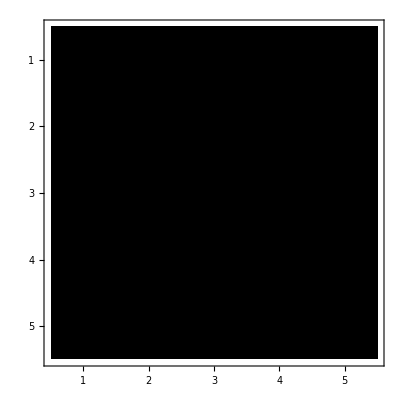
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[MatrixPlot[u/.InitialWMMs,PlotTheme->"Monochrome"],{u,Range[PlayerNum]}]
```

```mathematica
Table[MatrixPlot[u/.WMMs,PlotTheme->"Monochrome"],{u,Range[PlayerNum]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GamesTally
```

{{166,180,542},{161,178,548},{166,143,488},{150,157,480},{186,171,532}}

```mathematica
WinLoseRate=Table[N[(t[[1]]+t[[2]])/t[[3]]],{t,GamesTally}]
```

{0.638376,0.618613,0.633197,0.639583,0.671053}

```mathematica
DisparityRate=Table[Total[Table[Max[row],{row,lang/.InitialWMMs}]],{lang,Range[PlayerNum]}]
```

{1.58135,1.58135,1.58135,4.,4.}

```mathematica
FinalDisparityRate=Table[Total[Table[Max[row],{row,lang/.WMMs}]],{lang,Range[PlayerNum]}]
```

{4.89326,4.72375,5,4.89509,4.72144}

```mathematica
GetBestWordsForLang[lang_]:=Table[Flatten[Position[row,Max[row]]],{row,lang/.InitialWMMs}]//Flatten
```

```mathematica
MatrixForm[InitialAverageDifference=Table[Mean[Table[Abs[(lang1/.InitialWMMs)[[row,GetBestWordsForLang[lang1][[row]]]]-(langi/.InitialWMMs)[[row,GetBestWordsForLang[lang1][[row]]]]],{row,WordNum},{langi,Range[PlayerNum]}]],{lang1,Range[PlayerNum]}]]
```

(0. | 0. | 0. | 0.340625 | 0.340625
0. | 0. | 0. | 0.340625 | 0.340625
0. | 0. | 0. | 0.340625 | 0.340625
0.643272 | 0.643272 | 0.643272 | 0. | 0.
0.643272 | 0.643272 | 0.643272 | 0. | 0.)

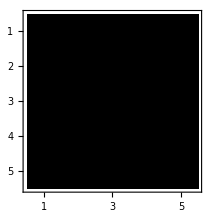

```mathematica
MatrixPlot[InitialAverageDifference,PlotTheme->"Monochrome"]
```

```mathematica
CommonLanguageIDs=Table[Flatten[Position[row,Max[row]]],{row,1/.WMMs}]//Flatten
```

{1,2,3,4,5}

```mathematica
Initial2CommonDifference=Table[Total[Table[1-((lang/.InitialWMMs)[[i,CommonLanguageIDs[[i]]]]),{i,WordNum}]],{lang,Range[PlayerNum]}]
```

{4.21636,4.21636,4.21636,1.,1.}

```mathematica
Learned2CommonDifference=Table[Total[Table[1-((lang/.WMMs)[[i,CommonLanguageIDs[[i]]]]),{i,WordNum}]],{lang,Range[PlayerNum]}]
```

{0.10674,0.276248,0,0.104912,0.278564}

```mathematica
Initial2CommonDifference-Learned2CommonDifference//Abs
```

{4.10962,3.94011,4.21636,0.895088,0.721436}

```mathematica
CommonLanguage=ConstantArray[0,{WordNum,MeanNum}]
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
Do[CommonLanguage[[i,CommonLanguageIDs[[i]]]]=1,{i,WordNum}]
```

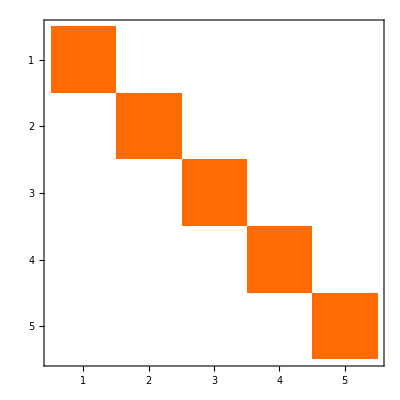

```mathematica
CommonLanguage//MatrixPlot
```